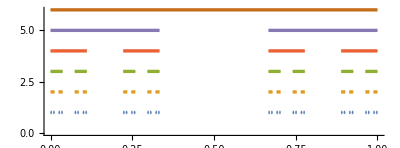

```mathematica
(* Raquel Lippincott - 2017
	Mathematica Notebook *)

Cantor[line_, it_, exitIt_] := 
If [it <= exitIt, {
Module[{length, line1, line2, pts1, pts2},
length = line[[2]] - line[[1]];
line1 = {line[[1]], line[[1]] + length/3.0};
line2 = {line[[1]] + 2.0*length/3.0,  line[[2]]};
pts1 = Flatten[Cantor[line1, it+1, exitIt]];
pts2 = Flatten[Cantor[line2, it+1, exitIt]];
Join[pts1, pts2]]
},{
line
}]

CantorSet[line_, iterations_] := 
If[iterations>0,
Interval@@Partition[Flatten[Cantor[line, 1, iterations]],2],
Interval[line]
]

CantorSetPlot[iterations_]:=
NumberLinePlot[Reverse[Table[CantorSet[{0,1},i],{i,0,iterations}]],PlotStyle->Directive[Thickness[0.006],PointSize[0]], ImageSize->Full]

CantorSetPlot[5]
```